```mathematica
A=1

J001=Table[u/.FindRoot[A×x^-1.5×ⅇ^(-J×x)×∑_(l=1)^10000 l^1.5×ⅇ^(-u×l)-1,{u,-0.001}],{J,0.5,5,0.5},{x,0.01,15,0.1}]
```

1

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{{6.90559,3.35604,2.4814,2.00614,1.6969,1.47606,1.30877,1.1767,1.0692,0.979614,0.903554,0.83799,0.780761,0.73028,0.685352,0.645058,0.60868,0.575644,0.54549,0.517839,0.492383,0.468859,0.447051,0.426773,0.407866,0.390194,0.373639,0.358098,0.343481,0.329709,0.316711,0.304425,0.292797,0.281775,0.271315,0.261378,0.251927,0.242929,0.234354,0.226174,0.218366,0.210905,0.203771,0.196945,0.190409,0.184147,0.178142,0.172383,0.166854,0.161544,0.156443,0.151538,0.146821,0.142282,0.137913,0.133705,0.129651,0.125745,0.121978,0.118345,0.11484,0.111457,0.108191,0.105038,0.101991,0.0990476,0.0962025,0.093452,0.0907922,0.0882195,0.0857305,0.0833219,0.0809905,0.0787335,0.076548,0.0744312,0.0723807,0.0703939,0.0684686,0.0666025,0.0647935,0.0630395,0.0613386,0.0596889,0.0580886,0.056536,0.0550294,0.0535674,0.0521483,0.0507707,0.0494332,0.0481346,0.0468734,0.0456485,0.0444587,0.0433029,0.0421799,0.0410887,0.0400282,0.0389976,0.0379958,0.037022,0.0360752,0.0351547,0.0342596,0.0333891,0.0325426,0.0317191,0.0309182,0.030139,0.0293809,0.0286433,0.0279256,0.0272272,0.0265474,0.0258859,0.025242,0.0246151,0.0240049,0.0234109,0.0228325,0.0222693,0.0217209,0.0211869,0.0206668,0.0201602,0.0196668,0.0191863,0.0187181,0.0182621,0.0178178,0.0173849,0.0169632,0.0165522,0.0161517,0.0157615,0.0153812,0.0150105,0.0146493,0.0142972,0.013954,0.0136194,0.0132933,0.0129754,0.0126654,0.0123632,0.0120686,0.0117813,0.0115011,0.011228},{6.90061,3.30624,2.3985,1.89984,1.57385,1.34078,1.16438,1.02547,0.912821,0.819384,0.740494,0.672926,0.614369,0.563121,0.517895,0.477701,0.441758,0.409448,0.380266,0.353801,0.329712,0.307715,0.287569,0.269069,0.25204,0.236331,0.221812,0.208366,0.195895,0.18431,0.173532,0.163493,0.154129,0.145386,0.137214,0.129569,0.122408,0.115697,0.109401,0.10349,0.0979375,0.0927172,0.0878063,0.0831836,0.0788297,0.0747268,0.0708582,0.067209,0.0637649,0.0605129,0.0574411,0.0545383,0.0517941,0.0491988,0.0467435,0.0444198,0.04222,0.0401368,0.0381634,0.0362935,0.0345211,0.0328408,0.0312472,0.0297356,0.0283014,0.0269403,0.0256483,0.0244216,0.0232567,0.0221502,0.021099,0.0201001,0.0191508,0.0182485,0.0173906,0.0165749,0.0157991,0.0150611,0.0143591,0.0136912,0.0130556,0.0124506,0.0118748,0.0113266,0.0108046,0.0103076,0.00983428,0.00938343,0.00895396,0.00854481,0.00815497,0.00778349,0.00742947,0.00709205,0.00677043,0.00646383,0.00617152,0.00589282,0.00562706,0.00537362,0.00513191,0.00490136,0.00468145,0.00447166,0.00427151,0.00408055,0.00389834,0.00372446,0.00355852,0.00340015,0.003249,0.00310471,0.00296698,0.00283549,0.00270996,0.00259011,0.00247566,0.00236638,0.00226203,0.00216236,0.00206718,0.00197627,0.00188943,0.00180648,0.00172724,0.00165154,0.00157922,0.00151012,0.0014441,0.001381,0.00132071,0.00126308,0.001208,0.00115533,0.00110498,0.00105682,0.00101075,0.000966655,0.000924442,0.000884009,0.00084526,0.000808101,0.000772444,0.000738201,0.000705288,0.000673626,0.000643138,0.00061375,0.000585395,0.000558005},{6.89562,3.25668,2.3172,1.79764,1.45814,1.21639,1.03458,0.892506,0.778302,0.684497,0.606128,0.539756,0.482914,0.433781,0.39098,0.353446,0.320345,0.291008,0.264895,0.241563,0.220646,0.201838,0.184881,0.169556,0.155676,0.143079,0.131626,0.121197,0.111685,0.102998,0.0950537,0.0877803,0.0811136,0.0749969,0.0693795,0.0642159,0.0594655,0.055092,0.0510623,0.0473469,0.0439192,0.0407547,0.0378317,0.0351303,0.0326323,0.0303213,0.0281822,0.0262015,0.0243665,0.0226659,0.0210893,0.019627,0.0182704,0.0170112,0.0158422,0.0147566,0.0137481,0.0128109,0.0119398,0.01113,0.0103768,0.00967623,0.0090244,0.00841779,0.00785314,0.00732743,0.00683788,0.00638192,0.00595716,0.00556138,0.00519255,0.00484878,0.0045283,0.00422949,0.00395085,0.00369096,0.00344854,0.00322237,0.00301134,0.00281441,0.00263061,0.00245904,0.00229887,0.00214932,0.00200968,0.00187927,0.00175747,0.00164369,0.0015374,0.00143809,0.00134528,0.00125854,0.00117745,0.00110161,0.00103064,0.000964198,0.000901933,0.000843521,0.00078865,0.000737023,0.00068836,0.000642398,0.000598889,0.000557608,0.000518344,0.000480905,0.000445118,0.000410824,0.000377881,0.00034616,0.000315547,0.000285938,0.000257241,0.000229372,0.000202258,0.000175832,0.000150035,0.000124812,0.000100116,0.0000759026,0.000052134,0.0000287746,5.79271×10^-6,-0.0000168405,-0.000039151,-0.0000611623,-0.000082896,-0.000104371,-0.000125606,-0.000146617,-0.000167419,-0.000188024,-0.000208446,-0.000228697,-0.000248785,-0.000268722,-0.000288515,-0.000308174,-0.000327705,-0.000347116,-0.000366413,-0.000385602,-0.000404689,-0.000423679,-0.000442577,-0.000461387,-0.000480113,-0.000498759,-0.000517329,-0.000535827},{6.89063,3.20737,2.23756,1.69961,1.34965,1.10244,0.918337,0.776047,0.663025,0.571358,0.495784,0.432658,0.379365,0.333975,0.295031,0.261406,0.232217,0.206763,0.184475,0.16489,0.147626,0.132365,0.118842,0.106831,0.0961423,0.0866123,0.0781012,0.0704885,0.0636698,0.0575544,0.0520633,0.0471272,0.0426857,0.0386852,0.0350789,0.0318252,0.0288873,0.0262327,0.0238325,0.0216608,0.0196948,0.0179139,0.0162998,0.0148361,0.0135083,0.0123031,0.0112087,0.0102146,0.00931113,0.00848979,0.00774283,0.00706327,0.00644484,0.00588186,0.0053692,0.00490223,0.00447675,0.00408899,0.00373549,0.00341317,0.00311919,0.00285101,0.0026063,0.00238297,0.0021791,0.00199297,0.00182299,0.00166774,0.00152591,0.00139631,0.00127785,0.00116954,0.00107045,0.000979696,0.000896474,0.000820013,0.00074959,0.00068453,0.00062421,0.000568063,0.000515578,0.000466301,0.000419831,0.000375817,0.000333953,0.000293975,0.000255654,0.000218793,0.000183221,0.000148789,0.000115371,0.000082855,0.0000511448,0.0000201565,-0.0000101831,-0.0000399384,-0.0000691657,-0.0000979145,-0.000126229,-0.000154147,-0.000181703,-0.000208929,-0.00023585,-0.000262492,-0.000288876,-0.000315021,-0.000340946,-0.000366666,-0.000392195,-0.000417547,-0.000442732,-0.000467763,-0.000492648,-0.000517396,-0.000542016,-0.000566515,-0.0005909,-0.000615177,-0.000639352,-0.00066343,-0.000687416,-0.000711315,-0.000735131,-0.000758868,-0.00078253,-0.00080612,-0.00082964,-0.000853095,-0.000876487,-0.000899818,-0.000923092,-0.000946309,-0.000969473,-0.000992585,-0.00101565,-0.00103866,-0.00106163,-0.00108455,-0.00110744,-0.00113027,-0.00115307,-0.00117583,-0.00119856,-0.00122124,-0.00124389,-0.00126651,-0.00128909,-0.00131164,-0.00133416,-0.00135664},{6.88565,3.15834,2.15962,1.60578,1.24823,0.998362,0.814546,0.674335,0.564494,0.476679,0.405353,0.346684,0.297928,0.257066,0.222579,0.193297,0.168308,0.146887,0.128456,0.112543,0.098763,0.0867993,0.0763876,0.0673074,0.0593734,0.0524287,0.0463404,0.0409953,0.0362963,0.0321604,0.0285159,0.0253013,0.0224629,0.0199546,0.0177361,0.0157724,0.0140329,0.012491,0.0111234,0.00990962,0.00883175,0.00787407,0.00702272,0.00626555,0.00559181,0.00499207,0.00445796,0.00398213,0.00355804,0.00317995,0.00284274,0.00254189,0.00227341,0.00203373,0.00181971,0.00162855,0.00145774,0.00130508,0.00116855,0.00104635,0.000936798,0.000838352,0.000749576,0.000669149,0.000595876,0.000528698,0.000466689,0.000409058,0.000355133,0.00030435,0.000256238,0.000210406,0.000166524,0.000124322,0.0000835689,0.000044075,5.67865×10^-6,-0.0000317564,-0.0000683458,-0.000104188,-0.000139367,-0.000173955,-0.000208014,-0.000241599,-0.000274755,-0.000307525,-0.000339944,-0.000372043,-0.000403849,-0.000435387,-0.00046668,-0.000497745,-0.0005286,-0.000559261,-0.000589741,-0.000620053,-0.000650208,-0.000680216,-0.000710086,-0.000739827,-0.000769446,-0.00079895,-0.000828345,-0.000857638,-0.000886834,-0.000915937,-0.000944953,-0.000973885,-0.00100274,-0.00103151,-0.00106022,-0.00108885,-0.00111742,-0.00114592,-0.00117437,-0.00120275,-0.00123108,-0.00125935,-0.00128757,-0.00131574,-0.00134386,-0.00137194,-0.00139997,-0.00142795,-0.00145589,-0.0014838,-0.00151166,-0.00153948,-0.00156727,-0.00159501,-0.00162273,-0.00165041,-0.00167805,-0.00170567,-0.00173325,-0.0017608,-0.00178832,-0.00181581,-0.00184328,-0.00187071,-0.00189812,-0.00192551,-0.00195286,-0.00198019,-0.0020075,-0.00203479,-0.00206205,-0.00208928,-0.0021165,-0.00214369},{6.88066,3.10958,2.08345,1.51614,1.15363,0.903533,0.722086,0.585681,0.480421,0.397565,0.331333,0.277737,0.233934,0.197842,0.167902,0.142922,0.121979,0.104345,0.0894441,0.0768114,0.0660716,0.0569179,0.0490985,0.0424055,0.036666,0.0317362,0.0274954,0.0238422,0.0206914,0.0179706,0.0156186,0.0135835,0.0118209,0.010293,0.00896745,0.00781667,0.00681689,0.00594773,0.00519165,0.00453355,0.00396043,0.00346106,0.00302573,0.00264604,0.00231475,0.00202557,0.00177303,0.00155242,0.0013596,0.00119097,0.00104334,0.000913803,0.000799738,0.000698735,0.000608638,0.000527556,0.000453882,0.000386277,0.000323645,0.0002651,0.000209929,0.000157558,0.000107527,0.0000594612,0.0000130593,-0.0000319256,-0.0000756959,-0.000118419,-0.000160232,-0.000201252,-0.000241576,-0.000281285,-0.000320449,-0.000359127,-0.00039737,-0.000435222,-0.000472719,-0.000509896,-0.000546781,-0.000583398,-0.000619771,-0.000655918,-0.000691857,-0.000727602,-0.000763169,-0.000798569,-0.000833813,-0.000868911,-0.000903873,-0.000938706,-0.000973418,-0.00100802,-0.00104251,-0.00107689,-0.00111118,-0.00114538,-0.00117949,-0.00121352,-0.00124746,-0.00128133,-0.00131513,-0.00134886,-0.00138252,-0.00141612,-0.00144965,-0.00148313,-0.00151654,-0.00154991,-0.00158321,-0.00161647,-0.00164968,-0.00168284,-0.00171596,-0.00174903,-0.00178205,-0.00181504,-0.00184798,-0.00188089,-0.00191375,-0.00194658,-0.00197937,-0.00201213,-0.00204485,-0.00207754,-0.0021102,-0.00214283,-0.00217542,-0.00220799,-0.00224052,-0.00227303,-0.00230551,-0.00233796,-0.00237039,-0.00240279,-0.00243517,-0.00246752,-0.00249984,-0.00253214,-0.00256442,-0.00259668,-0.00262891,-0.00266113,-0.00269332,-0.00272549,-0.00275764,-0.00278977,-0.00282188,-0.00285397,-0.00288605,-0.0029181},{6.87568,3.0611,2.00908,1.43068,1.0656,0.817303,0.639859,0.508518,0.408766,0.331517,0.270789,0.222476,0.18367,0.152252,0.12665,0.105671,0.0883998,0.0741226,0.062279,0.0524238,0.0442009,0.0373231,0.0315581,0.0267164,0.022643,0.0192105,0.0163139,0.0138663,0.0117955,0.0100416,0.00855456,0.00729256,0.0062206,0.0053093,0.00453398,0.00387389,0.00331151,0.00283207,0.00242311,0.00207406,0.00177598,0.00152131,0.00130358,0.00111727,0.000957511,0.000819983,0.000700781,0.000596455,0.000504043,0.000421099,0.000345659,0.000276181,0.000211461,0.000150569,0.0000927806,0.0000375314,-0.0000156221,-0.0000670303,-0.000116973,-0.000165674,-0.000213316,-0.000260047,-0.000305988,-0.000351241,-0.00039589,-0.000440005,-0.000483646,-0.000526863,-0.0005697,-0.000612193,-0.000654374,-0.000696272,-0.000737911,-0.000779311,-0.000820493,-0.000861471,-0.000902262,-0.000942877,-0.00098333,-0.00102363,-0.00106379,-0.00110381,-0.00114371,-0.00118348,-0.00122315,-0.0012627,-0.00130216,-0.00134152,-0.00138079,-0.00141997,-0.00145906,-0.00149808,-0.00153702,-0.00157589,-0.00161469,-0.00165342,-0.00169208,-0.00173069,-0.00176923,-0.00180772,-0.00184615,-0.00188453,-0.00192285,-0.00196113,-0.00199935,-0.00203753,-0.00207567,-0.00211376,-0.00215181,-0.00218981,-0.00222778,-0.00226571,-0.0023036,-0.00234145,-0.00237927,-0.00241705,-0.0024548,-0.00249251,-0.0025302,-0.00256785,-0.00260547,-0.00264306,-0.00268062,-0.00271815,-0.00275566,-0.00279314,-0.00283059,-0.00286802,-0.00290542,-0.00294279,-0.00298015,-0.00301747,-0.00305478,-0.00309206,-0.00312932,-0.00316656,-0.00320378,-0.00324097,-0.00327815,-0.0033153,-0.00335244,-0.00338956,-0.00342665,-0.00346373,-0.00350079,-0.00353783,-0.00357486,-0.00361187,-0.00364886,-0.00368583},{6.87069,3.01292,1.93655,1.34933,0.983806,0.739015,0.566826,0.441422,0.34774,0.276409,0.221289,0.1782,0.144199,0.117164,0.0955311,0.0781281,0.0640638,0.0526532,0.043364,0.0357791,0.0295696,0.0244741,0.020284,0.016832,0.0139831,0.0116285,0.00967958,0.0080644,0.00672423,0.00561104,0.00468546,0.00391515,0.00327352,0.00273863,0.0022924,0.00191987,0.00160866,0.00134849,0.00113076,0.000948118,0.000794112,0.00066303,0.000549936,0.000450745,0.000362227,0.000281905,0.000207915,0.00013886,0.000073695,0.000011631,-0.0000479321,-0.000105455,-0.000161296,-0.000215736,-0.000268996,-0.000321255,-0.000372654,-0.000423312,-0.000473324,-0.000522768,-0.000571712,-0.000620209,-0.000668309,-0.000716049,-0.000763466,-0.000810587,-0.00085744,-0.000904045,-0.000950424,-0.000996593,-0.00104257,-0.00108836,-0.00113399,-0.00117945,-0.00122477,-0.00126995,-0.00131501,-0.00135993,-0.00140474,-0.00144944,-0.00149404,-0.00153853,-0.00158293,-0.00162724,-0.00167146,-0.0017156,-0.00175967,-0.00180365,-0.00184756,-0.00189141,-0.00193518,-0.0019789,-0.00202255,-0.00206614,-0.00210967,-0.00215315,-0.00219657,-0.00223994,-0.00228326,-0.00232653,-0.00236976,-0.00241294,-0.00245607,-0.00249916,-0.00254221,-0.00258522,-0.00262819,-0.00267112,-0.00271402,-0.00275688,-0.0027997,-0.00284249,-0.00288525,-0.00292797,-0.00297066,-0.00301332,-0.00305595,-0.00309855,-0.00314112,-0.00318366,-0.00322618,-0.00326867,-0.00331113,-0.00335357,-0.00339598,-0.00343837,-0.00348073,-0.00352307,-0.00356538,-0.00360768,-0.00364995,-0.0036922,-0.00373443,-0.00377663,-0.00381882,-0.00386099,-0.00390314,-0.00394526,-0.00398737,-0.00402946,-0.00407154,-0.00411359,-0.00415563,-0.00419765,-0.00423965,-0.00428163,-0.0043236,-0.00436556,-0.00440749,-0.00444942},{6.86571,2.96504,1.86589,1.27202,0.907933,0.668023,0.502019,0.383119,0.295794,0.230443,0.180828,0.142729,0.113207,0.0901606,0.0720574,0.0577635,0.0464271,0.0374022,0.0301936,0.0244191,0.0197815,0.0160485,0.0130375,0.0106045,0.00863525,0.00703895,0.00574321,0.00469013,0.00383327,0.00313534,0.0025663,0.00210193,0.00172265,0.00141262,0.00115891,0.000950749,0.000778901,0.000635307,0.000513164,0.000407035,0.000312796,0.000227421,0.000148722,0.0000751152,5.45143×10^-6,-0.0000611155,-0.000125215,-0.000187321,-0.000247797,-0.000306922,-0.000364916,-0.000421951,-0.000478166,-0.000533674,-0.000588565,-0.000642916,-0.000696787,-0.000750232,-0.000803295,-0.000856013,-0.000908419,-0.00096054,-0.0010124,-0.00106402,-0.00111542,-0.00116662,-0.00121763,-0.00126846,-0.00131912,-0.00136963,-0.00141999,-0.00147022,-0.00152032,-0.00157029,-0.00162015,-0.0016699,-0.00171955,-0.00176909,-0.00181854,-0.0018679,-0.00191718,-0.00196637,-0.00201548,-0.00206452,-0.00211348,-0.00216238,-0.0022112,-0.00225997,-0.00230866,-0.0023573,-0.00240588,-0.00245441,-0.00250288,-0.0025513,-0.00259966,-0.00264798,-0.00269625,-0.00274447,-0.00279265,-0.00284079,-0.00288888,-0.00293693,-0.00298495,-0.00303292,-0.00308085,-0.00312875,-0.00317662,-0.00322444,-0.00327224,-0.00332,-0.00336773,-0.00341542,-0.00346309,-0.00351073,-0.00355833,-0.00360591,-0.00365346,-0.00370099,-0.00374848,-0.00379595,-0.0038434,-0.00389082,-0.00393821,-0.00398558,-0.00403293,-0.00408026,-0.00412756,-0.00417484,-0.0042221,-0.00426933,-0.00431655,-0.00436374,-0.00441092,-0.00445808,-0.00450521,-0.00455233,-0.00459943,-0.00464651,-0.00469357,-0.00474062,-0.001,-0.001,-0.00488165,-0.00492863,-0.00497559,-0.00502254,-0.00506947,-0.00511638,-0.00516328,-0.00521016},{6.86072,2.91748,1.79712,1.19865,0.837639,0.60371,0.44455,0.332481,0.251589,0.192113,0.14776,0.114317,0.0888756,0.0693802,0.0543513,0.0427069,0.0336457,0.0265686,0.0210233,0.0166659,0.0132334,0.0105235,0.00837987,0.00668108,0.00533267,0.00426081,0.00340763,0.0027277,0.00218522,0.00175196,0.00140558,0.00112828,0.000905507,0.000724941,0.000576058,0.000450312,0.00034122,0.000244119,0.00015574,0.0000738039,-3.28665×10^-6,-0.0000766679,-0.000147159,-0.000215362,-0.000281722,-0.000346578,-0.00041019,-0.000472759,-0.000534442,-0.000595367,-0.000655636,-0.00071533,-0.000774519,-0.000833259,-0.000891598,-0.000949575,-0.00100723,-0.00106458,-0.00112166,-0.00117849,-0.0012351,-0.00129149,-0.00134768,-0.00140368,-0.00145952,-0.00151519,-0.00157072,-0.0016261,-0.00168134,-0.00173646,-0.00179146,-0.00184635,-0.00190112,-0.0019558,-0.00201037,-0.00206485,-0.00211924,-0.00217355,-0.00222777,-0.00228191,-0.00233598,-0.00238998,-0.0024439,-0.00249776,-0.00255156,-0.00260529,-0.00265896,-0.00271257,-0.00276612,-0.00281963,-0.00287308,-0.00292647,-0.00297982,-0.00303312,-0.00308638,-0.00313958,-0.00319275,-0.00324587,-0.00329895,-0.00335199,-0.00340499,-0.00345796,-0.00351088,-0.00356377,-0.00361663,-0.00366945,-0.00372224,-0.00377499,-0.00382772,-0.00388041,-0.00393307,-0.0039857,-0.0040383,-0.00409088,-0.00414343,-0.00419595,-0.00424844,-0.00430091,-0.00435335,-0.00440577,-0.00445816,-0.00451053,-0.00456288,-0.0046152,-0.0046675,-0.00471978,-0.00477204,-0.001,-0.00487649,-0.00492869,-0.00498086,-0.00503302,-0.00508515,-0.00513727,-0.00518937,-0.00524145,-0.00529352,-0.00534556,-0.00539759,-0.0054496,-0.0055016,-0.00555358,-0.00560554,-0.00565749,-0.00570942,-0.00576134,-0.00581324,-0.00586512,-0.00591699,-0.00596885}}

```mathematica
J05 = J001[[1]]
J1 = J001[[2]]
J105 = J001[[3]]
J2=J001[[4]]
J205 = J001[[5]]
J3 = J001[[6]]
J305 = J001[[7]]
```

{6.90559,3.35604,2.4814,2.00614,1.6969,1.47606,1.30877,1.1767,1.0692,0.979614,0.903554,0.83799,0.780761,0.73028,0.685352,0.645058,0.60868,0.575644,0.54549,0.517839,0.492383,0.468859,0.447051,0.426773,0.407866,0.390194,0.373639,0.358098,0.343481,0.329709,0.316711,0.304425,0.292797,0.281775,0.271315,0.261378,0.251927,0.242929,0.234354,0.226174,0.218366,0.210905,0.203771,0.196945,0.190409,0.184147,0.178142,0.172383,0.166854,0.161544,0.156443,0.151538,0.146821,0.142282,0.137913,0.133705,0.129651,0.125745,0.121978,0.118345,0.11484,0.111457,0.108191,0.105038,0.101991,0.0990476,0.0962025,0.093452,0.0907922,0.0882195,0.0857305,0.0833219,0.0809905,0.0787335,0.076548,0.0744312,0.0723807,0.0703939,0.0684686,0.0666025,0.0647935,0.0630395,0.0613386,0.0596889,0.0580886,0.056536,0.0550294,0.0535674,0.0521483,0.0507707,0.0494332,0.0481346,0.0468734,0.0456485,0.0444587,0.0433029,0.0421799,0.0410887,0.0400282,0.0389976,0.0379958,0.037022,0.0360752,0.0351547,0.0342596,0.0333891,0.0325426,0.0317191,0.0309182,0.030139,0.0293809,0.0286433,0.0279256,0.0272272,0.0265474,0.0258859,0.025242,0.0246151,0.0240049,0.0234109,0.0228325,0.0222693,0.0217209,0.0211869,0.0206668,0.0201602,0.0196668,0.0191863,0.0187181,0.0182621,0.0178178,0.0173849,0.0169632,0.0165522,0.0161517,0.0157615,0.0153812,0.0150105,0.0146493,0.0142972,0.013954,0.0136194,0.0132933,0.0129754,0.0126654,0.0123632,0.0120686,0.0117813,0.0115011,0.011228}

{6.90061,3.30624,2.3985,1.89984,1.57385,1.34078,1.16438,1.02547,0.912821,0.819384,0.740494,0.672926,0.614369,0.563121,0.517895,0.477701,0.441758,0.409448,0.380266,0.353801,0.329712,0.307715,0.287569,0.269069,0.25204,0.236331,0.221812,0.208366,0.195895,0.18431,0.173532,0.163493,0.154129,0.145386,0.137214,0.129569,0.122408,0.115697,0.109401,0.10349,0.0979375,0.0927172,0.0878063,0.0831836,0.0788297,0.0747268,0.0708582,0.067209,0.0637649,0.0605129,0.0574411,0.0545383,0.0517941,0.0491988,0.0467435,0.0444198,0.04222,0.0401368,0.0381634,0.0362935,0.0345211,0.0328408,0.0312472,0.0297356,0.0283014,0.0269403,0.0256483,0.0244216,0.0232567,0.0221502,0.021099,0.0201001,0.0191508,0.0182485,0.0173906,0.0165749,0.0157991,0.0150611,0.0143591,0.0136912,0.0130556,0.0124506,0.0118748,0.0113266,0.0108046,0.0103076,0.00983428,0.00938343,0.00895396,0.00854481,0.00815497,0.00778349,0.00742947,0.00709205,0.00677043,0.00646383,0.00617152,0.00589282,0.00562706,0.00537362,0.00513191,0.00490136,0.00468145,0.00447166,0.00427151,0.00408055,0.00389834,0.00372446,0.00355852,0.00340015,0.003249,0.00310471,0.00296698,0.00283549,0.00270996,0.00259011,0.00247566,0.00236638,0.00226203,0.00216236,0.00206718,0.00197627,0.00188943,0.00180648,0.00172724,0.00165154,0.00157922,0.00151012,0.0014441,0.001381,0.00132071,0.00126308,0.001208,0.00115533,0.00110498,0.00105682,0.00101075,0.000966655,0.000924442,0.000884009,0.00084526,0.000808101,0.000772444,0.000738201,0.000705288,0.000673626,0.000643138,0.00061375,0.000585395,0.000558005}

{6.89562,3.25668,2.3172,1.79764,1.45814,1.21639,1.03458,0.892506,0.778302,0.684497,0.606128,0.539756,0.482914,0.433781,0.39098,0.353446,0.320345,0.291008,0.264895,0.241563,0.220646,0.201838,0.184881,0.169556,0.155676,0.143079,0.131626,0.121197,0.111685,0.102998,0.0950537,0.0877803,0.0811136,0.0749969,0.0693795,0.0642159,0.0594655,0.055092,0.0510623,0.0473469,0.0439192,0.0407547,0.0378317,0.0351303,0.0326323,0.0303213,0.0281822,0.0262015,0.0243665,0.0226659,0.0210893,0.019627,0.0182704,0.0170112,0.0158422,0.0147566,0.0137481,0.0128109,0.0119398,0.01113,0.0103768,0.00967623,0.0090244,0.00841779,0.00785314,0.00732743,0.00683788,0.00638192,0.00595716,0.00556138,0.00519255,0.00484878,0.0045283,0.00422949,0.00395085,0.00369096,0.00344854,0.00322237,0.00301134,0.00281441,0.00263061,0.00245904,0.00229887,0.00214932,0.00200968,0.00187927,0.00175747,0.00164369,0.0015374,0.00143809,0.00134528,0.00125854,0.00117745,0.00110161,0.00103064,0.000964198,0.000901933,0.000843521,0.00078865,0.000737023,0.00068836,0.000642398,0.000598889,0.000557608,0.000518344,0.000480905,0.000445118,0.000410824,0.000377881,0.00034616,0.000315547,0.000285938,0.000257241,0.000229372,0.000202258,0.000175832,0.000150035,0.000124812,0.000100116,0.0000759026,0.000052134,0.0000287746,5.79271×10^-6,-0.0000168405,-0.000039151,-0.0000611623,-0.000082896,-0.000104371,-0.000125606,-0.000146617,-0.000167419,-0.000188024,-0.000208446,-0.000228697,-0.000248785,-0.000268722,-0.000288515,-0.000308174,-0.000327705,-0.000347116,-0.000366413,-0.000385602,-0.000404689,-0.000423679,-0.000442577,-0.000461387,-0.000480113,-0.000498759,-0.000517329,-0.000535827}

{6.89063,3.20737,2.23756,1.69961,1.34965,1.10244,0.918337,0.776047,0.663025,0.571358,0.495784,0.432658,0.379365,0.333975,0.295031,0.261406,0.232217,0.206763,0.184475,0.16489,0.147626,0.132365,0.118842,0.106831,0.0961423,0.0866123,0.0781012,0.0704885,0.0636698,0.0575544,0.0520633,0.0471272,0.0426857,0.0386852,0.0350789,0.0318252,0.0288873,0.0262327,0.0238325,0.0216608,0.0196948,0.0179139,0.0162998,0.0148361,0.0135083,0.0123031,0.0112087,0.0102146,0.00931113,0.00848979,0.00774283,0.00706327,0.00644484,0.00588186,0.0053692,0.00490223,0.00447675,0.00408899,0.00373549,0.00341317,0.00311919,0.00285101,0.0026063,0.00238297,0.0021791,0.00199297,0.00182299,0.00166774,0.00152591,0.00139631,0.00127785,0.00116954,0.00107045,0.000979696,0.000896474,0.000820013,0.00074959,0.00068453,0.00062421,0.000568063,0.000515578,0.000466301,0.000419831,0.000375817,0.000333953,0.000293975,0.000255654,0.000218793,0.000183221,0.000148789,0.000115371,0.000082855,0.0000511448,0.0000201565,-0.0000101831,-0.0000399384,-0.0000691657,-0.0000979145,-0.000126229,-0.000154147,-0.000181703,-0.000208929,-0.00023585,-0.000262492,-0.000288876,-0.000315021,-0.000340946,-0.000366666,-0.000392195,-0.000417547,-0.000442732,-0.000467763,-0.000492648,-0.000517396,-0.000542016,-0.000566515,-0.0005909,-0.000615177,-0.000639352,-0.00066343,-0.000687416,-0.000711315,-0.000735131,-0.000758868,-0.00078253,-0.00080612,-0.00082964,-0.000853095,-0.000876487,-0.000899818,-0.000923092,-0.000946309,-0.000969473,-0.000992585,-0.00101565,-0.00103866,-0.00106163,-0.00108455,-0.00110744,-0.00113027,-0.00115307,-0.00117583,-0.00119856,-0.00122124,-0.00124389,-0.00126651,-0.00128909,-0.00131164,-0.00133416,-0.00135664}

{6.88565,3.15834,2.15962,1.60578,1.24823,0.998362,0.814546,0.674335,0.564494,0.476679,0.405353,0.346684,0.297928,0.257066,0.222579,0.193297,0.168308,0.146887,0.128456,0.112543,0.098763,0.0867993,0.0763876,0.0673074,0.0593734,0.0524287,0.0463404,0.0409953,0.0362963,0.0321604,0.0285159,0.0253013,0.0224629,0.0199546,0.0177361,0.0157724,0.0140329,0.012491,0.0111234,0.00990962,0.00883175,0.00787407,0.00702272,0.00626555,0.00559181,0.00499207,0.00445796,0.00398213,0.00355804,0.00317995,0.00284274,0.00254189,0.00227341,0.00203373,0.00181971,0.00162855,0.00145774,0.00130508,0.00116855,0.00104635,0.000936798,0.000838352,0.000749576,0.000669149,0.000595876,0.000528698,0.000466689,0.000409058,0.000355133,0.00030435,0.000256238,0.000210406,0.000166524,0.000124322,0.0000835689,0.000044075,5.67865×10^-6,-0.0000317564,-0.0000683458,-0.000104188,-0.000139367,-0.000173955,-0.000208014,-0.000241599,-0.000274755,-0.000307525,-0.000339944,-0.000372043,-0.000403849,-0.000435387,-0.00046668,-0.000497745,-0.0005286,-0.000559261,-0.000589741,-0.000620053,-0.000650208,-0.000680216,-0.000710086,-0.000739827,-0.000769446,-0.00079895,-0.000828345,-0.000857638,-0.000886834,-0.000915937,-0.000944953,-0.000973885,-0.00100274,-0.00103151,-0.00106022,-0.00108885,-0.00111742,-0.00114592,-0.00117437,-0.00120275,-0.00123108,-0.00125935,-0.00128757,-0.00131574,-0.00134386,-0.00137194,-0.00139997,-0.00142795,-0.00145589,-0.0014838,-0.00151166,-0.00153948,-0.00156727,-0.00159501,-0.00162273,-0.00165041,-0.00167805,-0.00170567,-0.00173325,-0.0017608,-0.00178832,-0.00181581,-0.00184328,-0.00187071,-0.00189812,-0.00192551,-0.00195286,-0.00198019,-0.0020075,-0.00203479,-0.00206205,-0.00208928,-0.0021165,-0.00214369}

{6.88066,3.10958,2.08345,1.51614,1.15363,0.903533,0.722086,0.585681,0.480421,0.397565,0.331333,0.277737,0.233934,0.197842,0.167902,0.142922,0.121979,0.104345,0.0894441,0.0768114,0.0660716,0.0569179,0.0490985,0.0424055,0.036666,0.0317362,0.0274954,0.0238422,0.0206914,0.0179706,0.0156186,0.0135835,0.0118209,0.010293,0.00896745,0.00781667,0.00681689,0.00594773,0.00519165,0.00453355,0.00396043,0.00346106,0.00302573,0.00264604,0.00231475,0.00202557,0.00177303,0.00155242,0.0013596,0.00119097,0.00104334,0.000913803,0.000799738,0.000698735,0.000608638,0.000527556,0.000453882,0.000386277,0.000323645,0.0002651,0.000209929,0.000157558,0.000107527,0.0000594612,0.0000130593,-0.0000319256,-0.0000756959,-0.000118419,-0.000160232,-0.000201252,-0.000241576,-0.000281285,-0.000320449,-0.000359127,-0.00039737,-0.000435222,-0.000472719,-0.000509896,-0.000546781,-0.000583398,-0.000619771,-0.000655918,-0.000691857,-0.000727602,-0.000763169,-0.000798569,-0.000833813,-0.000868911,-0.000903873,-0.000938706,-0.000973418,-0.00100802,-0.00104251,-0.00107689,-0.00111118,-0.00114538,-0.00117949,-0.00121352,-0.00124746,-0.00128133,-0.00131513,-0.00134886,-0.00138252,-0.00141612,-0.00144965,-0.00148313,-0.00151654,-0.00154991,-0.00158321,-0.00161647,-0.00164968,-0.00168284,-0.00171596,-0.00174903,-0.00178205,-0.00181504,-0.00184798,-0.00188089,-0.00191375,-0.00194658,-0.00197937,-0.00201213,-0.00204485,-0.00207754,-0.0021102,-0.00214283,-0.00217542,-0.00220799,-0.00224052,-0.00227303,-0.00230551,-0.00233796,-0.00237039,-0.00240279,-0.00243517,-0.00246752,-0.00249984,-0.00253214,-0.00256442,-0.00259668,-0.00262891,-0.00266113,-0.00269332,-0.00272549,-0.00275764,-0.00278977,-0.00282188,-0.00285397,-0.00288605,-0.0029181}

{6.87568,3.0611,2.00908,1.43068,1.0656,0.817303,0.639859,0.508518,0.408766,0.331517,0.270789,0.222476,0.18367,0.152252,0.12665,0.105671,0.0883998,0.0741226,0.062279,0.0524238,0.0442009,0.0373231,0.0315581,0.0267164,0.022643,0.0192105,0.0163139,0.0138663,0.0117955,0.0100416,0.00855456,0.00729256,0.0062206,0.0053093,0.00453398,0.00387389,0.00331151,0.00283207,0.00242311,0.00207406,0.00177598,0.00152131,0.00130358,0.00111727,0.000957511,0.000819983,0.000700781,0.000596455,0.000504043,0.000421099,0.000345659,0.000276181,0.000211461,0.000150569,0.0000927806,0.0000375314,-0.0000156221,-0.0000670303,-0.000116973,-0.000165674,-0.000213316,-0.000260047,-0.000305988,-0.000351241,-0.00039589,-0.000440005,-0.000483646,-0.000526863,-0.0005697,-0.000612193,-0.000654374,-0.000696272,-0.000737911,-0.000779311,-0.000820493,-0.000861471,-0.000902262,-0.000942877,-0.00098333,-0.00102363,-0.00106379,-0.00110381,-0.00114371,-0.00118348,-0.00122315,-0.0012627,-0.00130216,-0.00134152,-0.00138079,-0.00141997,-0.00145906,-0.00149808,-0.00153702,-0.00157589,-0.00161469,-0.00165342,-0.00169208,-0.00173069,-0.00176923,-0.00180772,-0.00184615,-0.00188453,-0.00192285,-0.00196113,-0.00199935,-0.00203753,-0.00207567,-0.00211376,-0.00215181,-0.00218981,-0.00222778,-0.00226571,-0.0023036,-0.00234145,-0.00237927,-0.00241705,-0.0024548,-0.00249251,-0.0025302,-0.00256785,-0.00260547,-0.00264306,-0.00268062,-0.00271815,-0.00275566,-0.00279314,-0.00283059,-0.00286802,-0.00290542,-0.00294279,-0.00298015,-0.00301747,-0.00305478,-0.00309206,-0.00312932,-0.00316656,-0.00320378,-0.00324097,-0.00327815,-0.0033153,-0.00335244,-0.00338956,-0.00342665,-0.00346373,-0.00350079,-0.00353783,-0.00357486,-0.00361187,-0.00364886,-0.00368583}

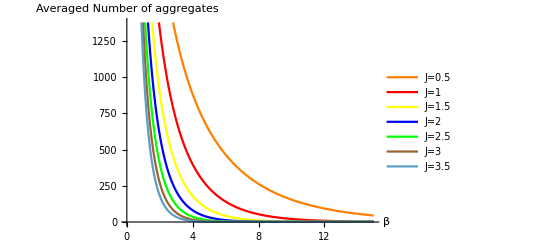

```mathematica
ListLinePlot[{(∑_(l=1)^10000 l^1.5×ⅇ^(-J05×l))/(∑_(l=1)^10000 l^2.5×ⅇ^(-J05×l))×10000,(∑_(l=1)^10000 l^1.5×ⅇ^(-J1×l))/(∑_(l=1)^10000 l^2.5×ⅇ^(-J1×l))×10000,(∑_(l=1)^10000 l^1.5×ⅇ^(-J105×l))/(∑_(l=1)^10000 l^2.5×ⅇ^(-J105×l))×10000,(∑_(l=1)^10000 l^1.5×ⅇ^(-J2×l))/(∑_(l=1)^10000 l^2.5×ⅇ^(-J2×l))×10000,(∑_(l=1)^10000 l^1.5×ⅇ^(-J205×l))/(∑_(l=1)^10000 l^2.5×ⅇ^(-J205×l))×10000,(∑_(l=1)^10000 l^1.5×ⅇ^(-J3×l))/(∑_(l=1)^10000 l^2.5×ⅇ^(-J3×l))×10000,(∑_(l=1)^10000 l^1.5×ⅇ^(-J305×l))/(∑_(l=1)^10000 l^2.5×ⅇ^(-J305×l))×10000},DataRange->{0,15},PlotStyle->{Orange,Red,Yellow,Blue,Green,Brown,Grey},PlotLegends->{"J=0.5","J=1","J=1.5","J=2","J=2.5","J=3","J=3.5"},AxesLabel->{"β","Averaged Number of aggregates"}]
```

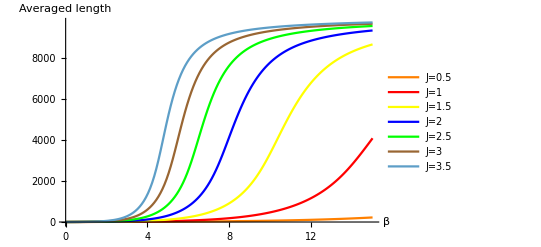

```mathematica
ListLinePlot[{(∑_(l=1)^10000 l^2.5×ⅇ^(-J05×l))/(∑_(l=1)^10000 l^1.5×ⅇ^(-J05×l)),(∑_(l=1)^10000 l^2.5×ⅇ^(-J1×l))/(∑_(l=1)^10000 l^1.5×ⅇ^(-J1×l)),(∑_(l=1)^10000 l^2.5×ⅇ^(-J105×l))/(∑_(l=1)^10000 l^1.5×ⅇ^(-J105×l)),(∑_(l=1)^10000 l^2.5×ⅇ^(-J2×l))/(∑_(l=1)^10000 l^1.5×ⅇ^(-J2×l)),(∑_(l=1)^10000 l^2.5×ⅇ^(-J205×l))/(∑_(l=1)^10000 l^1.5×ⅇ^(-J205×l)),(∑_(l=1)^10000 l^2.5×ⅇ^(-J3×l))/(∑_(l=1)^10000 l^1.5×ⅇ^(-J3×l)),(∑_(l=1)^10000 l^2.5×ⅇ^(-J305×l))/(∑_(l=1)^10000 l^1.5×ⅇ^(-J305×l))},DataRange->{0,15},PlotStyle->{Orange,Red,Yellow,Blue,Green,Brown,Grey},PlotLegends->{"J=0.5","J=1","J=1.5","J=2","J=2.5","J=3","J=3.5"},AxesLabel->{"β","Averaged length"}]
```